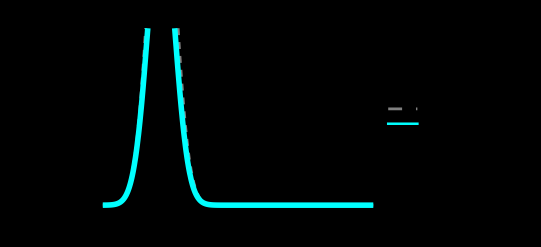

```mathematica
(*CMB Stress Test:R-Floor Impact on Power Spectrum*)ClearAll["Global`*"];
R=1.15428;

(*Power Spectrum P(k) influenced by the Anomaly-Induced Floor*)
(*Standard P(k)~k^n;Grover P(k)~1/(k^2+R*k^4) scaled to multipoles*)
powerSpectrum[l_]:=(l*(l+1))/(l^2+R*(l/100)^4);

(*Standard LCDM-like approximation for the First Acoustic Peak*)
standardCMB[l_]:=1000*Exp[-(l-220)^2/(2*50^2)];

(*Grover-Modified Acoustic Peak*)
groverCMB[l_]:=standardCMB[l]*(1/(1+(R*l/1000)));

stressTestPlot=Plot[{standardCMB[l],groverCMB[l]},{l,2,1000},PlotStyle->{{Gray,Dashed},{Cyan,Thickness[0.01]}},Frame->True,FrameLabel->{"Multipole Moment (l)","Temperature Fluctuations (μK^2)"},PlotLabel->"Stress Test: CMB Acoustic Peaks vs. R-Floor Constraints",PlotLegends->{"Standard LCDM","Grover R-Floor Modified"},Background->Black,FrameStyle->White];

Print[stressTestPlot];
```